```mathematica
M=10.^6;
k=10.^3;
m=10.^-3;
u=10.^-6;
n=10.^-9;
```

```mathematica
f[x_,m_]:=1000. x/m;
mm=360.;
J=1.;
```

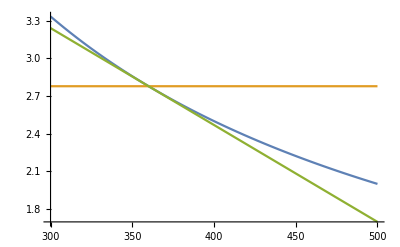

```mathematica
Plot[{f[J,m],f[J,mm],2.7777777777777777-0.00771604938271605 (m-360.)},{m,mm-60,mm+140}]
```

```mathematica
Series[f[J,m],{m,mm,1}]
```

2.77778-0.00771605 (m-360.)+O[m-360.]^2

```mathematica
k=17./18.*16/15.
```

1.00741

```mathematica
h[r_]:=(300.*227*10^-6)/r*k
```

```mathematica
h[22]*1000.
```

3.11838

```mathematica
(500*10^3)*(0.1*10^-6)
```

0.05

```mathematica
0.20*0.01*1000
```

2.

```mathematica
Sqrt[4.*300.*(1.38*10^-23)]*Sqrt[500*10^3]
```

9.09945×10^-8

```mathematica
30*10
```

300

```mathematica
35 + 30*3
```

125

```mathematica
3./29
```

0.103448

```mathematica
Rs=(Vs-Vr)/(Iq+Il)/.{Vs-> 3.3,Vr->2.5,Iq-> 100u,Il->0.1m}
```

4000.

```mathematica
(3.3-2.5)/4700.
```

0.000170213

```mathematica
P[R1_,R2_]:=(R1 R2)/(R1 + R2);
```

```mathematica
P[24k,1k]
```

960.

```mathematica
150n*100k
```

0.015

```mathematica
5*3m/0.9
```

0.0166667

```mathematica
20/30
```

2/3

```mathematica
25./30
```

0.833333

```mathematica
(1+(10m/2.5))
```

1.004

```mathematica
1. * 50m / 30
```

0.00166667

```mathematica
Rb=150k;
50n*Rb
200n*Rb
```

0.0075

0.03

```mathematica
RR[J_]:= J/(360u);
RR[3.118m]+450
```

458.661

```mathematica
3.118
```

```mathematica
JJ[R_]:=360u*(R - 450)HeavisideTheta[R - 450];
JJ[450+8.2]
```

0.002952

```mathematica
50u*100k
```

5.

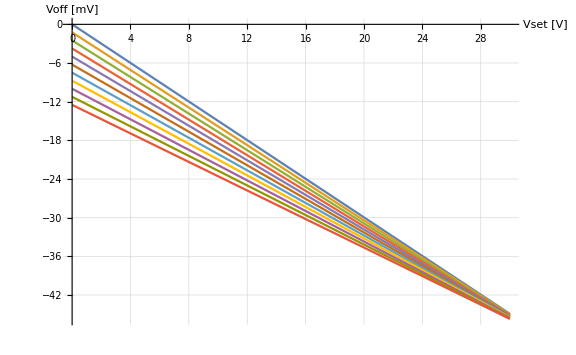

```mathematica
Plot[Evaluate@Table[(-Ib Rb + Ib Rb Vset/Vcc-μ Vset)k/.{Ib->25n,Vcc-> 32.,μ->1-(1M)/(1M+1.5k)},{Rb,0k,500k, 50k}],{Vset,0,30},AxesLabel->{"Vset [V]", "Voff [mV]"}, GridLines->Automatic,ImageSize->Large]
```

```mathematica
100./139.5
```

0.716846

```mathematica
3.3*0.1
```

0.33

```mathematica
100./30.
```

3.33333

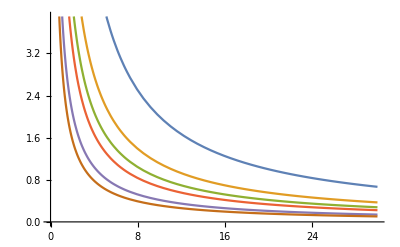

```mathematica
Plot[Evaluate@Table[100./(Vin*V),{Vin,{5,9,12,15,24,32}}], {V,0,30}]
```

```mathematica
Table[100./(30*V), {V,0,30,5}]
```

Power::infy: Infinite expression 1/0 encountered.

{ComplexInfinity,0.666667,0.333333,0.222222,0.166667,0.133333,0.111111}